```mathematica
Quit[];
```

```mathematica
(*parameter values for example in section 3.1 - Simulations in a theoretical context*)
tu=0.1;
tv=0.2;
bet=10;
ac=-19;
bc=10;
cc=10;
dc=-19;
```

```mathematica
(*function defining the Wilson-Cowan system*)
f[z_]:=1/(1+Exp[-bet*z]);
F[u_,ud_]:={
-u[[1]]+f[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium state*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{0.0478985,0.0511112}

```mathematica
(*characteristic parameter values*)
alpha=ac*f'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f'[tu+ac*eq[[1]]+bc*eq[[2]]]*f'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-17.8796

57.7268

```mathematica
(*Strong Gamma kernel - Laplace transform and related functions defined in paper*)
H[z_]:=(2/(2+z))^2;
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2*Re[Q[t,I*w]];
be[t_,w_]:=Abs[Q[t,I*w]]^2;
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=4/(4+w^2); (*given explicitely for ease of computation*)
theta[w_]:=2ArcTan[w/2]; (*given explicitely for ease of computation*)
w1[t_]:=2*Sqrt[1+t]; (*given explicitely for ease of computation*)
mu[w_]:=1/(rho[w]*Cos[theta[w]]);
```

```mathematica
(*Use Theorem 2.8 and Example 2.2 for the Strong Gamma kernel, to detect critical value of time delay and frequency - along the line (l_tau)*)
(*find critical value of tau based on the equation of the line (l_tau) from Example 2.2 *)
Tau=tau/.NSolve[beta==-((tau+2)^2/tau)*(alpha+(tau+2)^2/tau)&&tau>0,tau][[1]]
```

0.433992

```mathematica
(*compute wtau*)
wtau=w1[Tau]
```

2.39499

```mathematica
(*predicted frequency of oscillations at Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=wtau/(Tau*2*Pi)
```

0.878298

```mathematica
(*stability region for Strong Gamma kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared - using inequalities in Example 2.2*)
ps[t_]:=
Show[RegionPlot[y>-(2+t)^2/t(x+(2+t)^2/t)&&y<((-8+(-4+x) t)^2 (-2 x+(2+t)^2))/(4 t (4+t)^3)&&y>x-1,{x,2*mu[w1[t]],2},{y,mu[w1[t]],0.96*mu[w1[t]]^2},PlotPoints->100],
Plot[x-1,{x,1+1/Co[t,w1[t]],2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"S. Gamma, τ=",t}],Bold,19],Background->LightYellow,RoundingRadius->4],{1+mu[wtau],0.85*mu[wtau]^2}],
PlotRange->{{2*mu[wtau],2},{mu[wtau],0.96*mu[wtau]^2}}]
```

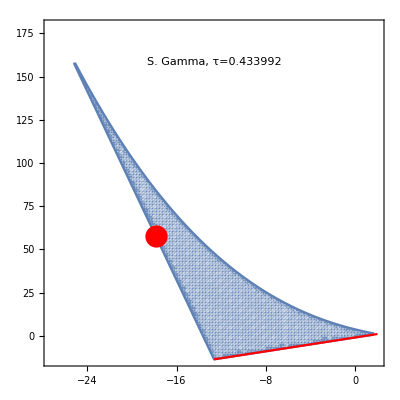

```mathematica
ps[Tau]
```

```mathematica
(*system with STRONG GAMMA kernel - using linear chain trick*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[2]],
ud1'[t]==2*(u[t]-ud1[t])/tau,
vd1'[t]==2*(v[t]-vd1[t])/tau,
ud2'[t]==2*(ud1[t]-ud2[t])/tau,
vd2'[t]==2*(vd1[t]-vd2[t])/tau,
u[0]==eq[[1]]*RandomReal[{0.1,0.2}],
v[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud1[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd1[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud2[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd2[0]==eq[[2]]*RandomReal[{0.1,0.2}]};
```

```mathematica
(*frequency at Hopf bifurcation computed based on the numerically evaluated solution - agrees with theoretically calculated value*)
Tmax=4000;
pts=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[1]],
v'[t]==F[{u[t],v[t]},{ud2[t],vd2[t]}][[2]],
ud1'[t]==2*(u[t]-ud1[t])/Tau,
vd1'[t]==2*(v[t]-vd1[t])/Tau,
ud2'[t]==2*(ud1[t]-ud2[t])/Tau,
vd2'[t]==2*(vd1[t]-vd2[t])/Tau,
u[0]==eq[[1]]*RandomReal[{0.1,0.2}],
v[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud1[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd1[0]==eq[[2]]*RandomReal[{0.1,0.2}],
ud2[0]==eq[[1]]*RandomReal[{0.1,0.2}],
vd2[0]==eq[[2]]*RandomReal[{0.1,0.2}],
WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,0.8*Tmax,Tmax}]][[2,1]];
frequency=1/Mean[Differences[pts,1,2]]
```

0.878077

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=20;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v,ud1,vd1,ud2,vd2},{t,Tmax}]],{t,0,Tmax-trans},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"u(t), v(t)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

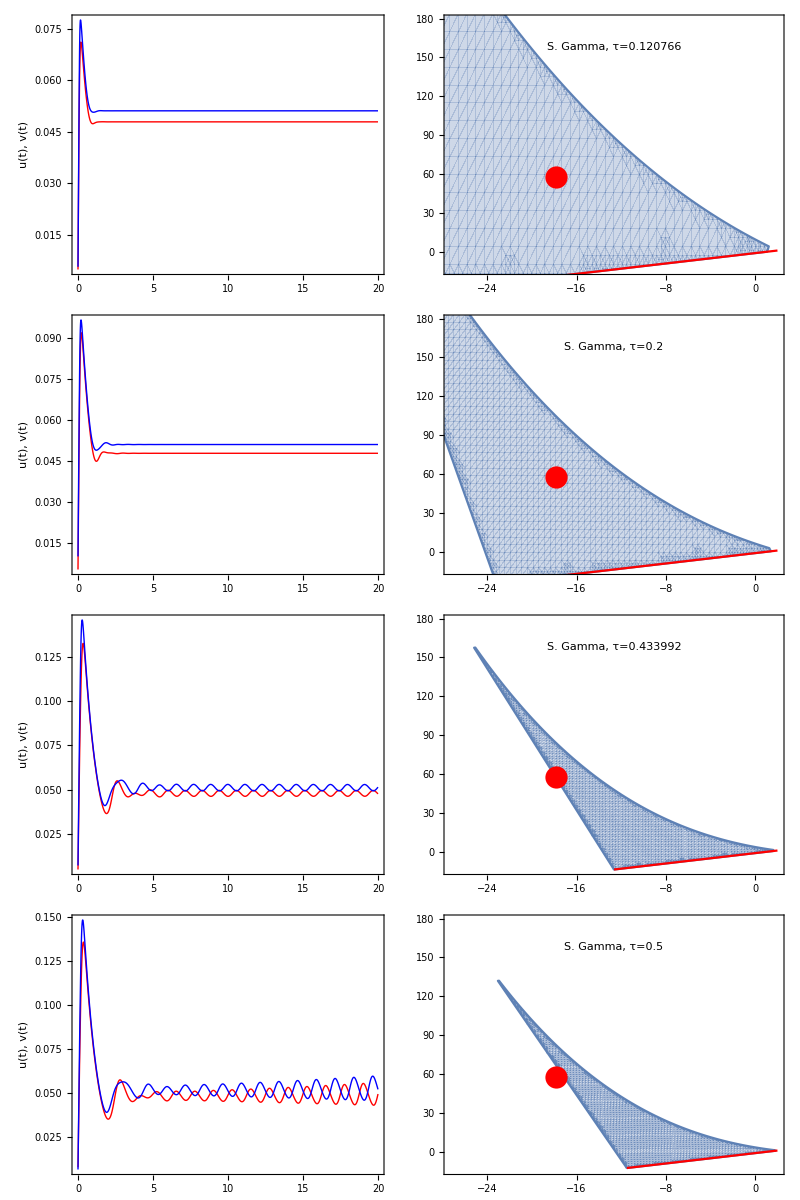

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[0.120766],ps[0.120766]},{p1[0.2],ps[0.2]},{p1[Tau],ps[Tau]},{p1[0.5],ps[0.5]}}]
```